```mathematica
(* This notebook solves both the baseline version of the Brock-Mirman model and an extension used originally in Final16 that adds a multiplier a la kmpHandbook *)
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
ParentDirectoryString = "..";SubDirectoryString = $PathnameSeparator;  (* Default for unix *)
OpenFigsUsingShell=False;
FullPageSize  = {72. 8.5  ,72. 8.5/GoldenRatio};
HalfPageSize  = {72. 6.5  ,72. 6.5/GoldenRatio};
ThirdPageSize = {72. 4.5  ,72. 4.5/GoldenRatio};
LandscapeSize = {72. 11.0,72. 7.5} //N;
ExportFigsToDir[FigName_,DirNameForFigs_] := Block[{},
  Print[Show[ToExpression[FigName]]];
  Print["Exporting figure to "<>DirNameForFigs<>SubDirectoryString<>FigName<>".xxx"];
  Export[DirNameForFigs <>          SubDirectoryString <> FigName <> ".eps", ToExpression[FigName], "EPS"];
  Export[DirNameForFigs <>          SubDirectoryString <> FigName <> ".jpg", ToExpression[FigName], "JPG"];
  Export[DirNameForFigs <>          SubDirectoryString <> FigName <> ".png", ToExpression[FigName], "PNG",ImageSize->FullPageSize];
  Export[DirNameForFigs <>          SubDirectoryString <> FigName <> ".svg", ToExpression[FigName], "SVG"]; (* SVG version causes a crash on Windows based systems ! *)
  Export[DirNameForFigs <>          SubDirectoryString <> FigName <> ".pdf", ToExpression[FigName], "PDF"];
  If[OpenFigsUsingShell != False, Run["open "<>DirNameForFigs <> SubDirectoryString <> FigName <> ".pdf"]];
];
```

```mathematica
Clear[α,β,ω,κ];κ=(1-α β);

(* *)
Clear[CFunc];CFunc[K_,A_] := κ A K^α;
Clear[cFunc];cFunc[k_,a_] := Log[1-α β] + a + α k;
Clear[YFunc];YFunc[K_,A_] :=  A K^α;
Clear[yFunc];yFunc[k_,a_] := a+α k;

Clear[MakeNext];
MakeNext := Block[{},
AppendTo[ZDyn,Exp[zDyn[[-1]]]];
AppendTo[aDyn,zDyn[[-1]]+ω cDyn[[-1]]];
AppendTo[ADyn,Exp[zDyn[[-1]]+ω cDyn[[-1]]]];
AppendTo[KDyn,SDyn[[-1]]];
AppendTo[kDyn,sDyn[[-1]]];
AppendTo[YDyn,YFunc[KDyn[[-1]],ADyn[[-1]]]];
AppendTo[yDyn,yFunc[kDyn[[-1]],aDyn[[-1]]]];
AppendTo[CDyn,CFunc[KDyn[[-1]],ADyn[[-1]]]];
AppendTo[cDyn,cFunc[kDyn[[-1]],aDyn[[-1]]]];
AppendTo[SDyn,(α β)YDyn[[-1]]];
AppendTo[sDyn,Log[α β]+yDyn[[-1]]];
AppendTo[tDyn,tDyn[[-1]]+1];
];

InitializeForSims[PreShockPer_] := Block[{},
ADyn={ASS};
aDyn={aSS};
ZDyn={1};
zDyn={0};
KDyn={KSS};
kDyn={kSS};
CDyn={CFunc[KSS,ASS]};
cDyn={cFunc[kSS,aSS]};
YDyn={YFunc[KSS,ASS]};
yDyn={yFunc[kSS,aSS]};
SDyn={(α β) YFunc[KSS,ASS]};
sDyn={Log[α β] +yFunc[kSS,aSS]};
tDyn={-PreShockPer+1};
];

SimUnitShockAfterPreShockPer[PreShockPer_,PostShockPer_] := Block[{},
Do[AppendTo[zDyn,0.];MakeNext;,{i,PreShockPer}];
Do[AppendTo[zDyn,1.];MakeNext;,{i,PostShockPer}];
];
(* Find the pseudo-steady-state solution to the model *)
ClearAll[α,β,ω,aSS,cSS,ySS,kSS,ASS,CSS,YSS,KSS,ss,SS];
(* See http://mathematica.stackexchange.com/questions/6669/assign-the-results-from-a-solve-to-variables *)
ss = Set @@@ Solve[{
aSS==ω cSS,
ySS==aSS+α kSS,
cSS== Log[1-α β] + ySS,
kSS==Log[α β]+ySS
},{aSS,cSS,ySS,kSS}] [[1]];
SS = {ASS,CSS,YSS,KSS}=Exp[ss];
Print[MatrixForm[Transpose[{{"aSS=","cSS=","ySS=","kSS="},ss}]]];
```

(aSS= | -(ω (α Log[α β]+Log[1-α β]-α Log[1-α β]))/(-1+α+ω)
cSS= | -(α Log[α β]+Log[1-α β]-α Log[1-α β])/(-1+α+ω)
ySS= | -(α Log[α β]+ω Log[1-α β])/(-1+α+ω)
kSS= | -(Log[α β]-ω Log[α β]+ω Log[1-α β])/(-1+α+ω))

```mathematica
PreShkPerBase=2;
PostShkPerBase=7;
```

```mathematica
(* Now do analytical work to calculate growth rates after a period-0 shock *)
InitializeForSims[PreShkPerAnalytical=0];
AppendTo[zDyn,ζ];MakeNext;
AppendTo[zDyn,ζ];MakeNext;
AppendTo[zDyn,ζ];MakeNext;
AppendTo[zDyn,ζ];MakeNext;
```

```mathematica
{Simplify[yDyn[[2]]-yDyn[[1]]],Simplify[yDyn[[3]]-yDyn[[2]]],Simplify[yDyn[[4]]-yDyn[[3]]],Simplify[yDyn[[5]]-yDyn[[4]]]}
```

{ζ,ζ (α+ω),ζ (α+ω)^2,ζ (α+ω)^3}

```mathematica
{Simplify[aDyn[[2]]-aDyn[[1]]],Simplify[aDyn[[3]]-aDyn[[2]]],Simplify[aDyn[[4]]-aDyn[[3]]],Simplify[aDyn[[5]]-aDyn[[4]]]}
```

{ζ,ζ ω,ζ ω (α+ω),ζ ω (α+ω)^2}

```mathematica
α=0.3;
β=0.99;
ω=0.3;
InitializeForSims[PreShkPerBase]; (* Now that paramter values have been defined, this will be numerical *)
SimUnitShockAfterPreShockPer[PreShkPerBase,PostShkPerBase];
Clear[MaxGapVert]; (* Needed to ensure scale is comparable on graphs being compared *)
aGapVert=aDyn[[-1]]-aDyn[[1]];
yGapVert=yDyn[[-1]]-yDyn[[1]];
kGapVert=kDyn[[-1]]-kDyn[[1]];
MaxGapVert=Max[aGapVert,yGapVert,kGapVert];
```

```mathematica
PlotDyn[•Dyn_,•Name_,PlotStyleVal_,PreShkPer_,GapVert_] := 
ListPlot[Transpose[{tDyn,•Dyn}]
,AxesLabel->{"t",•Name}
,Ticks->{{{PreShkPer,"1"}},None}
,PlotStyle->PlotStyleVal
,Axes->True
,AxesOrigin->{-(PreShkPer-1),•Dyn[[1]]}
,PlotRange->{Automatic,{-GapVert/50,1.05GapVert}}
];
yPlotMultYes=PlotDyn[yDyn-yDyn[[1]],"y",Red,PreShkPerBase,MaxGapVert];
kPlotMultYes=PlotDyn[kDyn-kDyn[[1]],"k",Red,PreShkPerBase,MaxGapVert];
aPlotMultYes=PlotDyn[aDyn-aDyn[[1]],"a",Red,PreShkPerBase,MaxGapVert];
```

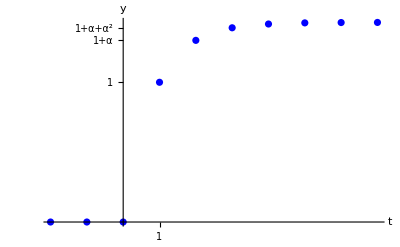

Exporting figure to /Volumes/Data/Courses/Choice/LectureNotes/DSGEModels/Handouts/BrockMirman/Figures/yPlotBrockMirman.xxx

```mathematica
ω=0.0;
InitializeForSims[PreShkPerBase]; (* Now that parameter values have been defined, this will be numerical *)
SimUnitShockAfterPreShockPer[PreShkPerBase,PostShkPerBase];
yPlotMultNo=PlotDyn[yDyn-yDyn[[1]],"y",Blue,PreShkPerBase,MaxGapVert];

kPlotMultNo=PlotDyn[kDyn-kDyn[[1]],"k",Blue,PreShkPerBase,MaxGapVert];
aPlotMultNo=PlotDyn[aDyn-aDyn[[1]],"a",Blue,PreShkPerBase,MaxGapVert];
yPlotMultYvsN = Show[{yPlotMultNo,yPlotMultYes}];
kPlotMultYvsN=Show[{kPlotMultNo,kPlotMultYes}];aPlotMultYvsN=Show[{aPlotMultNo,aPlotMultYes}];
PlotDynBrockMirman[•Dyn_,•Name_,PlotStyleVal_,PreShkPer_,GapVert_] := 
ListPlot[Transpose[{tDyn,•Dyn}]
,AxesLabel->{"t",•Name}
,Ticks->{{{PreShkPer,"1"}},{{1.,"1"},{1+α,"1+α"},{1+α+α^2,"1+α+α^2"}}}
,PlotStyle->PlotStyleVal
,Axes->True
,AxesOrigin->{1,•Dyn[[1]]}
,PlotRange->{Automatic,{-GapVert/50,1.05GapVert}}
];
yPlotBrockMirman=PlotDynBrockMirman[yDyn-yDyn[[1]],"y",Blue,PreShkPerBase,yDyn-yDyn[[1]]];
ExportFigsToDir["yPlotBrockMirman","/Volumes/Data/Courses/Choice/LectureNotes/DSGEModels/Handouts/BrockMirman/Figures"];
```

```mathematica
Transpose[{tDyn,yDyn-yDyn[[1]]}]
```

{{-1,0.},{0,0.},{1,0.},{2,1.},{3,1.3},{4,1.39},{5,1.417},{6,1.4251},{7,1.42753},{8,1.42826}}

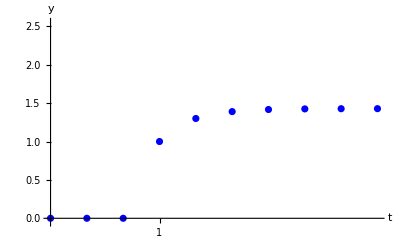

Exporting figure to /Volumes/Data/Courses/Choice/LectureNotes/DSGEModels/Handouts/BrockMirman/Figures/yPlotMultNo.xxx

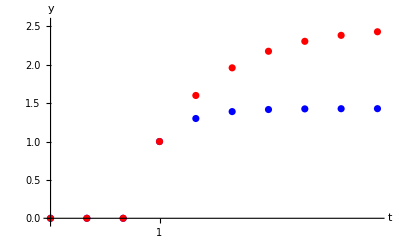

Exporting figure to /Volumes/Data/Courses/Choice/LectureNotes/DSGEModels/Handouts/BrockMirman/Figures/yPlotMultYvsN.xxx

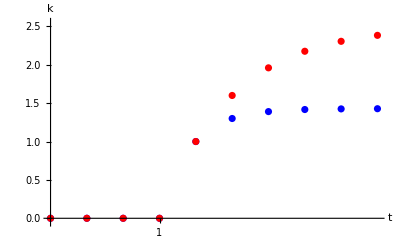

Exporting figure to /Volumes/Data/Courses/Choice/LectureNotes/DSGEModels/Handouts/BrockMirman/Figures/kPlotMultYvsN.xxx

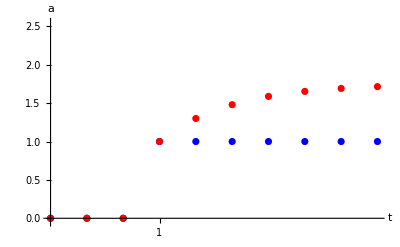

Exporting figure to /Volumes/Data/Courses/Choice/LectureNotes/DSGEModels/Handouts/BrockMirman/Figures/aPlotMultYvsN.xxx

```mathematica
FigsToExport={"yPlotMultNo","yPlotMultYvsN","kPlotMultYvsN","aPlotMultYvsN"};
Do[ExportFigsToDir[FigsToExport[[i]],"/Volumes/Data/Courses/Choice/LectureNotes/DSGEModels/Handouts/BrockMirman/Figures"],{i,Length[FigsToExport]}]
```

```mathematica
(* Now do an approximate version of the idea in the last question, about what things look like if there is gradual decay of the multiplier *)
```

```mathematica
α=0.3;
β=0.99;
ω=0.3;

InitializeForSims[PreShkPerBase]; (* Now that parameter values have been defined, this will be numerical *)
SimUnitShockAfterPreShockPer[PreShkPerBase,PostShkPerBase*5];
{yDynMultY,kDynMultY,aDynMultY}={yDyn-ySS,kDyn-kSS,aDyn-aSS};
```

```mathematica
α=0.3;
β=0.99;
ω=0.;

InitializeForSims[PreShkPerBase]; (* Now that parameter values have been defined, this will be numerical *)
SimUnitShockAfterPreShockPer[PreShkPerBase,PostShkPerBase*5];
{yDynMultN,kDynMultN,aDynMultN}={yDyn-ySS,kDyn-kSS,aDyn-aSS};
```

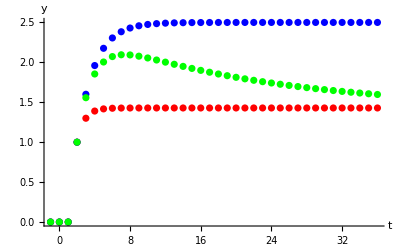

Exporting figure to /Volumes/Data/Courses/Choice/LectureNotes/DSGEModels/Handouts/BrockMirman/Figures/yPlotMix.xxx

```mathematica
λ=0.95;
Per=Length[kDyn];
Λ=Table[1.,{PreShkPerBase}];
Do[AppendTo[Λ,λ^i],{i,Per-PreShkPerBase}];
yDynMix=Λ yDynMultY + (1-Λ) yDynMultN;
yDynMultNPlot=ListPlot[Transpose[{tDyn,yDynMultN}],PlotStyle->Red,Ticks->{Automatic,None},AxesOrigin->{Automatic,ySS}];
yDynMultYPlot=ListPlot[Transpose[{tDyn,yDynMultY}],PlotStyle->Blue,Ticks->{Automatic,None},AxesOrigin->{Automatic,ySS}];
yDynMixPlot=ListPlot[Transpose[{tDyn,yDynMix}],PlotStyle->Green,Ticks->{Automatic,None},AxesOrigin->{Automatic,ySS}];
yPlotMix=Show[{yDynMultNPlot,yDynMultYPlot,yDynMixPlot},PlotRange->All,AxesLabel->{"t","y"}];
ExportFigsToDir["yPlotMix","/Volumes/Data/Courses/Choice/LectureNotes/DSGEModels/Handouts/BrockMirman/Figures"]
```